```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ServiceLine`"];
```

```mathematica
arrival = Import["Data/Arrival.dat"];
service = Import["Data/Server.dat"];
```

```mathematica
arrivalTime = Table[arrival[[i,2]],{i,2,Length[arrival]}];
serviceTime = Table[service[[i,2]],{i,2,Length[service]}];
queueLength = Table[{service[[i,1]],service[[i,5]]},{i,2,Length[service]}];
busyPercent = Table[{arrival[[i,1]],arrival[[i,4]]},{i,3,Length[arrival]}];
```

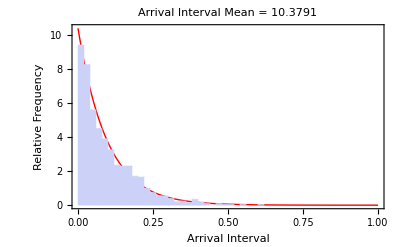

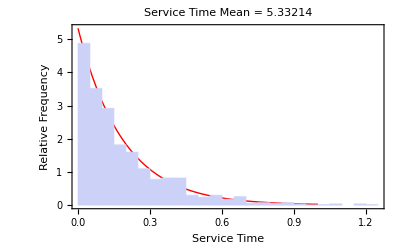

```mathematica
ExponentialFit[arrivalTime,{"Arrival Interval", "Relative Frequency"}]
ExponentialFit[serviceTime,{"Service Time", "Relative Frequency"}]
```

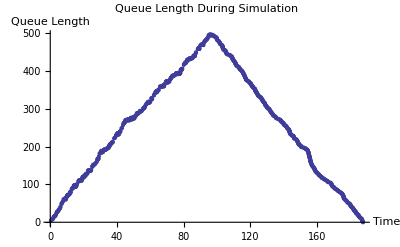

```mathematica
ListPlot[queueLength,AxesLabel->{"Time","Queue Length"},PlotLabel->"Queue Length During Simulation"]
```

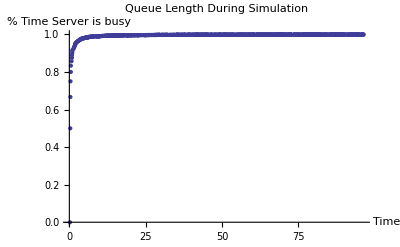

```mathematica
ListPlot[busyPercent,AxesLabel->{"Time","% Time Server is busy"},PlotLabel->"Queue Length During Simulation"]
```